```mathematica
plotAlignmentPhaseDiagram[file_] := Module[{data},
SetDirectory[NotebookDirectory[]];
data = Check[Import[file, "Table"], Return["Unable to import file"]];
ListPlot[data, PlotRange->Full, Joined->True, Mesh->All, Frame->True, FrameLabel->{{"Mean fraction on top", None}, {"Diffusion Dr", None}}, LabelStyle->15, ImageSize->400]
];
```

```mathematica
To plot the alignment phase diagram, first create a text file containing your interaction range-alignment data, with one entry per line:

...
0.2  0.167
0.3  0.461
0.4  0.738
...

Then enter the filename into the line below and evaluate.
```

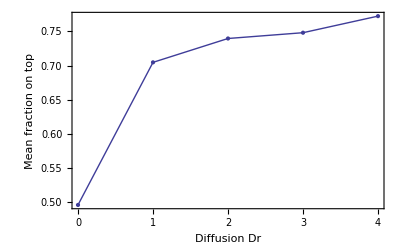

```mathematica
plotAlignmentPhaseDiagram["mean vs angle.txt"]
```